# アイゲンファクター

## アイゲンファクターとは

雑誌を評価する指標

たくさん引用される雑誌からの引用はそうでない雑誌からの引用に比べより価値をもつ、と言う考えが反映される(インパクトファクターとの違い)

Google PageRank算出の手法が応用される

トムソン・ロイターの Journal Citation Report で各誌のアイゲンファクターを見ることができる

インパクトファクターとの違い -> 雑誌により引用の重さが違う

Google PageRankとの違い -> Google PageRankでは、ランダムに遷移する確率を一様にしているのに対し、アイゲンファクターではこれを雑誌記事数に応じた確率にしている

## Nav: top

## アニメーションによるアイゲンファクターの算出の説明:

## See also

インパクトファクター

5年インパクトファクター

以上、webコンテンツ

## Programs

### google page soce

```mathematica
zeroSelf[mat_]:=Module[
{len,rl},
len=Length[mat];
rl=Table[{n,n}->0,{n,len}];
ReplacePart[mat,rl]
]
```

```mathematica
nextscore[{mat_,r_}]:={mat,Map[Tr,Transpose[(mat r)]]}
```

```mathematica
linkMatToH[mat_]:=Block[
{links},
links=Map[Tr,mat];
mat/links/.{Indeterminate->0}
]
```

```mathematica
hToG[mat_,alpha_]:=Block[
{n,zerolines,a,elem},
n=Length[mat];
zerolines=Position[Map[Tr,mat],0];
a=ReplacePart[Table[0,{n}],zerolines->1];
elem=Table[1,{n}];
mat*alpha+(alpha*a+(1-alpha)elem)*1/n
(*Transpose[Transpose[mat]*alpha+(alpha*a+(1-alpha)elem)*1/n]*)
]
```

```mathematica
googlePageScore[linkmat_,alpha_,itr_]:=Block[
{n,rstart,h,g},
n=Length[linkmat];
rstart=Table[1/n,{n}];
h=linkMatToH[linkmat];
g=hToG[h,alpha];
Nest[nextscore,{g,rstart},itr]
]
```

### Eigen factor

```mathematica
hToE[mat_,alpha_,w_]:=Block[
{n,zerolines,a,elem},
n=Length[mat];
zerolines=Position[Map[Tr,mat],0];
a=ReplacePart[Table[0,{n}],zerolines->1];
(*elem=Table[1,{n}];*)
elem=w/Tr[w]*n;
Transpose[Transpose[mat]*alpha+(alpha*a+(1-alpha)elem)*1/n]
]
```

```mathematica
eigenPageScore[linkmat_,alpha_,w_,itr_]:=Block[
{n,rstart,h,g},
n=Length[linkmat];
rstart=Table[1/n,{n}];
h=linkMatToH[linkmat];
g=hToE[h,alpha,w];
Nest[nextscore,{g,rstart},itr]
]
```

## 仮想的な雑誌5誌の例

```mathematica
journalNames={"A","B","C","D","E"}
```

{A,B,C,D,E}

被引用引用行列

```mathematica
(citedcitingV={
{20,3,4,10,12},
{10,30,15,13,5},
{3,2,10,3,8},
{2,1,50,60,17},
{10,9,25,3,40}
})
```

{{20,3,4,10,12},{10,30,15,13,5},{3,2,10,3,8},{2,1,50,60,17},{10,9,25,3,40}}

```mathematica
citingcitedV=Transpose[citedcitingV]
```

{{20,10,3,2,10},{3,30,2,1,9},{4,15,10,50,25},{10,13,3,60,3},{12,5,8,17,40}}

スライド0

```mathematica
regend[0]=Text["仮想的な5誌の引用被引用行列:  列が引用ベクトルとなる"]
```

仮想的な5誌の引用被引用行列:  列が引用ベクトルとなる

```mathematica
slide[0]=Grid[{{"","被引用"},{"引用",TableForm[citedcitingV,TableHeadings->{journalNames,journalNames}]},{regend[0],SpanFromLeft}}]
```

| 被引用
引用 |  | A | B | C | D | E
A | 20 | 3 | 4 | 10 | 12
B | 10 | 30 | 15 | 13 | 5
C | 3 | 2 | 10 | 3 | 8
D | 2 | 1 | 50 | 60 | 17
E | 10 | 9 | 25 | 3 | 40
仮想的な5誌の引用被引用行列:  列が引用ベクトルとなる |

自誌引用を0に置き換え

```mathematica
(citedcitingVzeroSelf=zeroSelf[citedcitingV])//TableForm
```

0 | 3 | 4 | 10 | 12
10 | 0 | 15 | 13 | 5
3 | 2 | 0 | 3 | 8
2 | 1 | 50 | 0 | 17
10 | 9 | 25 | 3 | 0

```mathematica
citingcitedVzeroSelf=Transpose[citedcitingVzeroSelf]
```

{{0,10,3,2,10},{3,0,2,1,9},{4,15,0,50,25},{10,13,3,0,3},{12,5,8,17,0}}

スライド1

```mathematica
regend[1]=Text["自誌引用を0に置き換えた引用被引用行列"]
```

自誌引用を0に置き換えた引用被引用行列

```mathematica
slide[1]=Grid[{{"","被引用"},{"引用",TableForm[citedcitingVzeroSelf,TableHeadings->{journalNames,journalNames}]},{regend[1],SpanFromLeft}}]
```

| 被引用
引用 |  | A | B | C | D | E
A | 0 | 3 | 4 | 10 | 12
B | 10 | 0 | 15 | 13 | 5
C | 3 | 2 | 0 | 3 | 8
D | 2 | 1 | 50 | 0 | 17
E | 10 | 9 | 25 | 3 | 0
自誌引用を0に置き換えた引用被引用行列 |

```mathematica
Map[Tr,citedcitingVzeroSelf]
```

{29,43,16,70,47}

```mathematica
w={25,56,33,28,45}
```

{25,56,33,28,45}

```mathematica
a=w/Tr[w]//N
```

{0.13369,0.299465,0.176471,0.149733,0.240642}

結果の確認

```mathematica
eps=eigenPageScore[Transpose[citedcitingVzeroSelf],0.85,a,30]
```

{{{0.0200535,0.38492,0.128471,0.0904599,0.376096},{0.190053,0.0449198,0.139804,0.0791266,0.546096},{0.0562237,0.180558,0.0264706,0.474588,0.26216},{0.313157,0.425954,0.114402,0.0224599,0.124027},{0.262911,0.14611,0.188375,0.366508,0.0360963}},{0.18448,0.226792,0.130604,0.19681,0.261314}}

```mathematica
Round[eps[[2]],0.00001]
```

{0.18448,0.22679,0.1306,0.19681,0.26131}

```mathematica
eps[[2]]//Tr
```

1.

各ステップに分解

```mathematica
citedcitingV//TableForm
```

20 | 3 | 4 | 10 | 12
10 | 30 | 15 | 13 | 5
3 | 2 | 10 | 3 | 8
2 | 1 | 50 | 60 | 17
10 | 9 | 25 | 3 | 40

自誌引用を0に置き換え

```mathematica
citedcitingVzeroSelf//TableForm
```

0 | 3 | 4 | 10 | 12
10 | 0 | 15 | 13 | 5
3 | 2 | 0 | 3 | 8
2 | 1 | 50 | 0 | 17
10 | 9 | 25 | 3 | 0

```mathematica
citingcitedVzeroself=Transpose[citedcitingVzeroSelf]
```

{{0,10,3,2,10},{3,0,2,1,9},{4,15,0,50,25},{10,13,3,0,3},{12,5,8,17,0}}

引用を比率で表す(引用の合計が1になる)

```mathematica
(citingcitedVzeroSelfH=linkMatToH[citingcitedVzeroself]//N)//TableForm
```

0. | 0.4 | 0.12 | 0.08 | 0.4
0.2 | 0. | 0.133333 | 0.0666667 | 0.6
0.0425532 | 0.159574 | 0. | 0.531915 | 0.265957
0.344828 | 0.448276 | 0.103448 | 0. | 0.103448
0.285714 | 0.119048 | 0.190476 | 0.404762 | 0.

トータルを確認

```mathematica
Map[Tr,citingcitedZeroSelfH]
```

citingcitedZeroSelfH

引用をたどって遷移する確率を0.85とする

```mathematica
(citingcitedVzeroSelfHa=0.85citingcitedVzeroSelfH)//TableForm
```

0. | 0.34 | 0.102 | 0.068 | 0.34
0.17 | 0. | 0.113333 | 0.0566667 | 0.51
0.0361702 | 0.135638 | 0. | 0.452128 | 0.226064
0.293103 | 0.381034 | 0.087931 | 0. | 0.087931
0.242857 | 0.10119 | 0.161905 | 0.344048 | 0.

トータルを確認

```mathematica
Map[Tr,citingcitedVzeroSelfHa]
```

{0.85,0.85,0.85,0.85,0.85}

ランダムに遷移する確率をaに掛ける

```mathematica
(1-0.85)a//Tr
```

0.15

それを引用遷移確率の行列に足す

```mathematica
citingcitedVzeroSelfE=Transpose[Transpose[citingcitedVzeroSelfHa]+(1-0.85)a]
```

{{0.0200535,0.38492,0.128471,0.0904599,0.376096},{0.190053,0.0449198,0.139804,0.0791266,0.546096},{0.0562237,0.180558,0.0264706,0.474588,0.26216},{0.313157,0.425954,0.114402,0.0224599,0.124027},{0.262911,0.14611,0.188375,0.366508,0.0360963}}

```mathematica
Map[Tr,citingcitedVzeroSelfE]
```

{1.,1.,1.,1.,1.}

繰り返し計算により点数を求める

```mathematica
citingcitedVzeroSelfG[30]=Nest[nextscore,{citingcitedVzeroSelfE,1/5},30]
```

{{{0.0200535,0.38492,0.128471,0.0904599,0.376096},{0.190053,0.0449198,0.139804,0.0791266,0.546096},{0.0562237,0.180558,0.0264706,0.474588,0.26216},{0.313157,0.425954,0.114402,0.0224599,0.124027},{0.262911,0.14611,0.188375,0.366508,0.0360963}},{0.18448,0.226792,0.130604,0.19681,0.261314}}

```mathematica
eps[[2]]-citingcitedVzeroSelfG[30][[2]]
```

{0.,0.,0.,0.,0.}

## 仮想的な雑誌5誌のスライド(引用被引用行列)

```mathematica
journalNames={"A","B","C","D","E"}
```

{A,B,C,D,E}

被引用引用行列

```mathematica
(citedcitingV={
{20,3,4,10,12},
{10,30,15,13,5},
{3,2,10,3,8},
{2,1,50,60,17},
{10,9,25,3,40}
})
```

{{20,3,4,10,12},{10,30,15,13,5},{3,2,10,3,8},{2,1,50,60,17},{10,9,25,3,40}}

```mathematica
citingcitedV=Transpose[citedcitingV]
```

{{20,10,3,2,10},{3,30,2,1,9},{4,15,10,50,25},{10,13,3,60,3},{12,5,8,17,40}}

#### スライド0

```mathematica
regend[0]=Text["上のような、仮想的な5誌の引用被引用行列よりアイゲン
ファクターを求めてみる。列が引用ベクトルとなる行列である。"]
```

上のような、仮想的な5誌の引用被引用行列よりアイゲン
ファクターを求めてみる。列が引用ベクトルとなる行列である。

```mathematica
slide[0]=Grid[{{"","被引用"},{"引用",TableForm[citingcitedV,TableHeadings->{journalNames,journalNames}]},{regend[0],SpanFromLeft}}]
```

| 被引用
引用 |  | A | B | C | D | E
A | 20 | 10 | 3 | 2 | 10
B | 3 | 30 | 2 | 1 | 9
C | 4 | 15 | 10 | 50 | 25
D | 10 | 13 | 3 | 60 | 3
E | 12 | 5 | 8 | 17 | 40
上のような、仮想的な5誌の引用被引用行列よりアイゲン
ファクターを求めてみる。列が引用ベクトルとなる行列である。 |

自誌引用を0に置き換え

```mathematica
(citedcitingVzeroSelf=zeroSelf[citedcitingV])//TableForm
```

0 | 3 | 4 | 10 | 12
10 | 0 | 15 | 13 | 5
3 | 2 | 0 | 3 | 8
2 | 1 | 50 | 0 | 17
10 | 9 | 25 | 3 | 0

```mathematica
citingcitedVzeroSelf=Transpose[citedcitingVzeroSelf]
```

{{0,10,3,2,10},{3,0,2,1,9},{4,15,0,50,25},{10,13,3,0,3},{12,5,8,17,0}}

#### スライド1

```mathematica
regend[1]=Text["つぎに、自誌引用を0に置き換えた行列を得る。"]
```

つぎに、自誌引用を0に置き換えた行列を得る。

```mathematica
slide[1]=Grid[{{"","被引用"},{"引用",TableForm[citingcitedVzeroSelf,TableHeadings->{journalNames,journalNames}]},{regend[1],SpanFromLeft}}]
```

| 被引用
引用 |  | A | B | C | D | E
A | 0 | 10 | 3 | 2 | 10
B | 3 | 0 | 2 | 1 | 9
C | 4 | 15 | 0 | 50 | 25
D | 10 | 13 | 3 | 0 | 3
E | 12 | 5 | 8 | 17 | 0
つぎに、自誌引用を0に置き換えた行列を得る。 |

```mathematica
Map[Tr,citedcitingVzeroSelf]
```

{29,43,16,70,47}

```mathematica
w={25,56,33,28,45}
```

{25,56,33,28,45}

```mathematica
a=w/Tr[w]//N
```

{0.13369,0.299465,0.176471,0.149733,0.240642}

結果の確認

```mathematica
eps=eigenPageScore[Transpose[citedcitingVzeroSelf],0.85,a,30]
```

{{{0.0200535,0.38492,0.128471,0.0904599,0.376096},{0.190053,0.0449198,0.139804,0.0791266,0.546096},{0.0562237,0.180558,0.0264706,0.474588,0.26216},{0.313157,0.425954,0.114402,0.0224599,0.124027},{0.262911,0.14611,0.188375,0.366508,0.0360963}},{0.18448,0.226792,0.130604,0.19681,0.261314}}

```mathematica
Round[eps[[2]],0.00001]
```

{0.18448,0.22679,0.1306,0.19681,0.26131}

```mathematica
eps[[2]]//Tr
```

1.

#### スライド2

```mathematica
citingcitedVzeroself=Transpose[citedcitingVzeroSelf]
```

{{0,10,3,2,10},{3,0,2,1,9},{4,15,0,50,25},{10,13,3,0,3},{12,5,8,17,0}}

引用を比率で表す(引用の合計が1になる)

```mathematica
(citingcitedVzeroSelfH=linkMatToH[citingcitedVzeroself]//N)//TableForm
```

0. | 0.4 | 0.12 | 0.08 | 0.4
0.2 | 0. | 0.133333 | 0.0666667 | 0.6
0.0425532 | 0.159574 | 0. | 0.531915 | 0.265957
0.344828 | 0.448276 | 0.103448 | 0. | 0.103448
0.285714 | 0.119048 | 0.190476 | 0.404762 | 0.

```mathematica
citedcitingVzeroSelfH=Transpose[citingcitedVzeroSelfH]
```

{{0.,0.2,0.0425532,0.344828,0.285714},{0.4,0.,0.159574,0.448276,0.119048},{0.12,0.133333,0.,0.103448,0.190476},{0.08,0.0666667,0.531915,0.,0.404762},{0.4,0.6,0.265957,0.103448,0.}}

トータルを確認

```mathematica
Map[Tr,citingcitedVzeroSelfH]
```

{1.,1.,1.,1.,1.}

```mathematica
regend[2]=Text["つぎに、引用(行)の合計を規格化した行列を得る。各行の
合計は1になる。"]
```

つぎに、引用(行)の合計を規格化した行列を得る。各行の
合計は1になる。

```mathematica
slide[2]=Grid[{{"","被引用"},{"引用",TableForm[Round[citingcitedVzeroSelfH,0.001],TableHeadings->{journalNames,journalNames}]},{regend[2],SpanFromLeft}}]
```

| 被引用
引用 |  | A | B | C | D | E
A | 0. | 0.4 | 0.12 | 0.08 | 0.4
B | 0.2 | 0. | 0.133 | 0.067 | 0.6
C | 0.043 | 0.16 | 0. | 0.532 | 0.266
D | 0.345 | 0.448 | 0.103 | 0. | 0.103
E | 0.286 | 0.119 | 0.19 | 0.405 | 0.
つぎに、引用(行)の合計を規格化した行列を得る。各行の
合計は1になる。 |

引用をたどって遷移する確率を0.85とする

```mathematica
(citingcitedVzeroSelfHa=0.85citingcitedVzeroSelfH)//TableForm
```

0. | 0.34 | 0.102 | 0.068 | 0.34
0.17 | 0. | 0.113333 | 0.0566667 | 0.51
0.0361702 | 0.135638 | 0. | 0.452128 | 0.226064
0.293103 | 0.381034 | 0.087931 | 0. | 0.087931
0.242857 | 0.10119 | 0.161905 | 0.344048 | 0.

#### スライド3

```mathematica
regend[3]=Text["次に、引用を辿って遷移する確率を0.85とするため、行列全外に
0.85を掛ける。"]
```

次に、引用を辿って遷移する確率を0.85とするため、行列全外に
0.85を掛ける。

```mathematica
slide[3]=Grid[{{"","被引用"},{"引用",TableForm[Round[citingcitedVzeroSelfHa,0.001],TableHeadings->{journalNames,journalNames}]},{regend[3],SpanFromLeft}}]
```

| 被引用
引用 |  | A | B | C | D | E
A | 0. | 0.34 | 0.102 | 0.068 | 0.34
B | 0.17 | 0. | 0.113 | 0.057 | 0.51
C | 0.036 | 0.136 | 0. | 0.452 | 0.226
D | 0.293 | 0.381 | 0.088 | 0. | 0.088
E | 0.243 | 0.101 | 0.162 | 0.344 | 0.
次に、引用を辿って遷移する確率を0.85とするため、行列全外に
0.85を掛ける。 |

引用トータルを確認

```mathematica
Map[Tr,citingcitedVzeroSelfHa]
```

{0.85,0.85,0.85,0.85,0.85}

ランダムに遷移する確率をaに掛ける

```mathematica
(1-0.85)a
```

{0.0200535,0.0449198,0.0264706,0.0224599,0.0360963}

```mathematica
(1-0.85)a//Tr
```

0.15

ベクトルaの各要素値を行列の各列の要素に足す

```mathematica
addMat=(Round[Table[(1-0.85)a,{5}],0.001]//TableForm)
```

0.02 | 0.045 | 0.026 | 0.022 | 0.036
0.02 | 0.045 | 0.026 | 0.022 | 0.036
0.02 | 0.045 | 0.026 | 0.022 | 0.036
0.02 | 0.045 | 0.026 | 0.022 | 0.036
0.02 | 0.045 | 0.026 | 0.022 | 0.036

```mathematica
addMat=TableForm[Round[Table[(1-0.85)a,{5}],0.001],TableHeadings->{journalNames,journalNames}]
```

| A | B | C | D | E
A | 0.02 | 0.045 | 0.026 | 0.022 | 0.036
B | 0.02 | 0.045 | 0.026 | 0.022 | 0.036
C | 0.02 | 0.045 | 0.026 | 0.022 | 0.036
D | 0.02 | 0.045 | 0.026 | 0.022 | 0.036
E | 0.02 | 0.045 | 0.026 | 0.022 | 0.036

#### スライド4

```mathematica
regend[4]=Text["つぎに、記事数に応じた確率を、行列の各被引用値に足す。
Google PageRankとの違いは、この確率にある。Google 
PageRankでは一様確率を足す。"]
```

つぎに、記事数に応じた確率を、行列の各被引用値に足す。
Google PageRankとの違いは、この確率にある。Google 
PageRankでは一様確率を足す。

```mathematica
slide[4]=Grid[{{"","被引用"},
{"引用",TableForm[Round[citingcitedVzeroSelfHa,0.001],TableHeadings->{journalNames,journalNames}]},
{Text[Style["+",Large]],SpanFromLeft},
{"記事数に
応じた
遷移確率",addMat},
{regend[4],SpanFromLeft}}]
```

| 被引用
引用 |  | A | B | C | D | E
A | 0. | 0.34 | 0.102 | 0.068 | 0.34
B | 0.17 | 0. | 0.113 | 0.057 | 0.51
C | 0.036 | 0.136 | 0. | 0.452 | 0.226
D | 0.293 | 0.381 | 0.088 | 0. | 0.088
E | 0.243 | 0.101 | 0.162 | 0.344 | 0.
+ | 
記事数に
応じた
遷移確率 |  | A | B | C | D | E
A | 0.02 | 0.045 | 0.026 | 0.022 | 0.036
B | 0.02 | 0.045 | 0.026 | 0.022 | 0.036
C | 0.02 | 0.045 | 0.026 | 0.022 | 0.036
D | 0.02 | 0.045 | 0.026 | 0.022 | 0.036
E | 0.02 | 0.045 | 0.026 | 0.022 | 0.036
つぎに、記事数に応じた確率を、行列の各被引用値に足す。
Google PageRankとの違いは、この確率にある。Google 
PageRankでは一様確率を足す。 |

#### スライド5

```mathematica
citingcitedVzeroSelfE=Transpose[Transpose[citingcitedVzeroSelfHa]+(1-0.85)a]
```

{{0.0200535,0.38492,0.128471,0.0904599,0.376096},{0.190053,0.0449198,0.139804,0.0791266,0.546096},{0.0562237,0.180558,0.0264706,0.474588,0.26216},{0.313157,0.425954,0.114402,0.0224599,0.124027},{0.262911,0.14611,0.188375,0.366508,0.0360963}}

```mathematica
citingcitedVzeroSelfEwithTotalciting=Map[Append[#,1.]&,citingcitedVzeroSelfE]
```

{{0.0200535,0.38492,0.128471,0.0904599,0.376096,1.},{0.190053,0.0449198,0.139804,0.0791266,0.546096,1.},{0.0562237,0.180558,0.0264706,0.474588,0.26216,1.},{0.313157,0.425954,0.114402,0.0224599,0.124027,1.},{0.262911,0.14611,0.188375,0.366508,0.0360963,1.}}

```mathematica
regend[5]=Text["これで、引用を辿って遷移する確率と、記事数に応じてランダムに遷移
する確率を足した(引用)確率行列が得られた。各行が引用確率ベクトル
(合計が1)は1になる。これに対して、Google PageRankと同じ繰り
返し法により最終的な点数を得る。"]
```

これで、引用を辿って遷移する確率と、記事数に応じてランダムに遷移
する確率を足した(引用)確率行列が得られた。各行が引用確率ベクトル
(合計が1)は1になる。これに対して、Google PageRankと同じ繰り
返し法により最終的な点数を得る。

```mathematica
slide[5]=Grid[{{"","被引用"},{"引用",TableForm[Round[citingcitedVzeroSelfEwithTotalciting,0.001],TableHeadings->{journalNames,Append[journalNames,"合計"]}]},{regend[5],SpanFromLeft}}]
```

| 被引用
引用 |  | A | B | C | D | E | 合計
A | 0.02 | 0.385 | 0.128 | 0.09 | 0.376 | 1.
B | 0.19 | 0.045 | 0.14 | 0.079 | 0.546 | 1.
C | 0.056 | 0.181 | 0.026 | 0.475 | 0.262 | 1.
D | 0.313 | 0.426 | 0.114 | 0.022 | 0.124 | 1.
E | 0.263 | 0.146 | 0.188 | 0.367 | 0.036 | 1.
これで、引用を辿って遷移する確率と、記事数に応じてランダムに遷移
する確率を足した(引用)確率行列が得られた。各行が引用確率ベクトル
(合計が1)は1になる。これに対して、Google PageRankと同じ繰り
返し法により最終的な点数を得る。 |

```mathematica
Map[Tr,citingcitedVzeroSelfE]
```

{1.,1.,1.,1.,1.}

```mathematica
Transpose[Transpose[citingcitedVzeroSelfHa]+{a1,a2,a3,a4,a5}]//TableForm
```

0.+a1 | 0.34+a2 | 0.102+a3 | 0.068+a4 | 0.34+a5
0.17+a1 | 0.+a2 | 0.113333+a3 | 0.0566667+a4 | 0.51+a5
0.0361702+a1 | 0.135638+a2 | 0.+a3 | 0.452128+a4 | 0.226064+a5
0.293103+a1 | 0.381034+a2 | 0.087931+a3 | 0.+a4 | 0.087931+a5
0.242857+a1 | 0.10119+a2 | 0.161905+a3 | 0.344048+a4 | 0.+a5

```mathematica
{{b,b},{d,d}}+{f,g}
```

{{b+f,b+f},{d+g,d+g}}

繰り返し計算により点数を求める

```mathematica
citingcitedVzeroSelfG[30]=Nest[nextscore,{citingcitedVzeroSelfE,1/5},30]
```

{{{0.0200535,0.38492,0.128471,0.0904599,0.376096},{0.190053,0.0449198,0.139804,0.0791266,0.546096},{0.0562237,0.180558,0.0264706,0.474588,0.26216},{0.313157,0.425954,0.114402,0.0224599,0.124027},{0.262911,0.14611,0.188375,0.366508,0.0360963}},{0.18448,0.226792,0.130604,0.19681,0.261314}}

```mathematica
citingcitedVzeroSelfG[30]
```

{{{0.0200535,0.38492,0.128471,0.0904599,0.376096},{0.190053,0.0449198,0.139804,0.0791266,0.546096},{0.0562237,0.180558,0.0264706,0.474588,0.26216},{0.313157,0.425954,0.114402,0.0224599,0.124027},{0.262911,0.14611,0.188375,0.366508,0.0360963}},{0.18448,0.226792,0.130604,0.19681,0.261314}}

```mathematica
Map[Tr[#]&,citingcitedVzeroSelfG[30][[1]]]
```

{1.,1.,1.,1.,1.}

```mathematica
citingcitedVzeroSelfG[30][[2]]
```

{0.18448,0.226792,0.130604,0.19681,0.261314}

```mathematica
finalTab[30]=citingcitedVzeroSelfG[30][[1]]*citingcitedVzeroSelfG[30][[2]]
```

{{0.00369946,0.0710099,0.0237002,0.016688,0.0693822},{0.0431026,0.0101874,0.0317064,0.0179453,0.12385},{0.00734305,0.0235817,0.00345717,0.0619832,0.0342392},{0.0616325,0.0838322,0.0225154,0.00442034,0.0244098},{0.0687022,0.0381806,0.0492251,0.0957735,0.00943245}}

```mathematica
finalTabwithTotal[30]=Transpose[Append[Transpose[Append[finalTab[30],citingcitedVzeroSelfG[30][[2]]]],Append[citingcitedVzeroSelfG[30][[2]],1.]]]
```

{{0.00369946,0.0710099,0.0237002,0.016688,0.0693822,0.18448},{0.0431026,0.0101874,0.0317064,0.0179453,0.12385,0.226792},{0.00734305,0.0235817,0.00345717,0.0619832,0.0342392,0.130604},{0.0616325,0.0838322,0.0225154,0.00442034,0.0244098,0.19681},{0.0687022,0.0381806,0.0492251,0.0957735,0.00943245,0.261314},{0.18448,0.226792,0.130604,0.19681,0.261314,1.}}

```mathematica
finalTabwithTotal[30]//TableForm
```

0.00369946 | 0.0710099 | 0.0237002 | 0.016688 | 0.0693822 | 0.18448
0.0431026 | 0.0101874 | 0.0317064 | 0.0179453 | 0.12385 | 0.226792
0.00734305 | 0.0235817 | 0.00345717 | 0.0619832 | 0.0342392 | 0.130604
0.0616325 | 0.0838322 | 0.0225154 | 0.00442034 | 0.0244098 | 0.19681
0.0687022 | 0.0381806 | 0.0492251 | 0.0957735 | 0.00943245 | 0.261314
0.18448 | 0.226792 | 0.130604 | 0.19681 | 0.261314 | 1.

```mathematica
Map[Tr[#]&,citingcitedVzeroSelfG[30][[1]]*citingcitedVzeroSelfG[30][[2]]]
```

{0.18448,0.226792,0.130604,0.19681,0.261314}

```mathematica
eps[[2]]-citingcitedVzeroSelfG[30][[2]]
```

{0.,0.,0.,0.,0.}

#### スライド6

```mathematica
regend[6]=Text["最終的に、確率行列にさらに得点を掛け込んだ「得点行列」を得る。
合計得点が高いほど重要な雑誌とされる。"]
```

最終的に、確率行列にさらに得点を掛け込んだ「得点行列」を得る。
合計得点が高いほど重要な雑誌とされる。

```mathematica
slide[6]=Grid[{{"","被引用"},{"引用",TableForm[Round[finalTabwithTotal[30],0.001],TableHeadings->{Append[journalNames,"合計"],Append[journalNames,"合計"]}]},{regend[6],SpanFromLeft}}]
```

| 被引用
引用 |  | A | B | C | D | E | 合計
A | 0.004 | 0.071 | 0.024 | 0.017 | 0.069 | 0.184
B | 0.043 | 0.01 | 0.032 | 0.018 | 0.124 | 0.227
C | 0.007 | 0.024 | 0.003 | 0.062 | 0.034 | 0.131
D | 0.062 | 0.084 | 0.023 | 0.004 | 0.024 | 0.197
E | 0.069 | 0.038 | 0.049 | 0.096 | 0.009 | 0.261
合計 | 0.184 | 0.227 | 0.131 | 0.197 | 0.261 | 1.
最終的に、確率行列にさらに得点を掛け込んだ「得点行列」を得る。
合計得点が高いほど重要な雑誌とされる。 |

#### スライド

```mathematica
animlist={slide[0],slide[1],slide[2],slide[3],slide[4],slide[5],slide[6]};
```

```mathematica
ListAnimate[animlist]
```

## 有機化学誌6誌の例

まず、結果の確認

```mathematica
(citedcitingZeroSelf={
{0,257,135,7,310,303},
{166,0,1768,325,2061,1641},
{161,2966,0,454,2185,2096},
{1,252,163,0,214,133},
{131,1207,788,196,0,1150},
{172,1442,967,175,1913,0}
})//TableForm
```

0 | 257 | 135 | 7 | 310 | 303
166 | 0 | 1768 | 325 | 2061 | 1641
161 | 2966 | 0 | 454 | 2185 | 2096
1 | 252 | 163 | 0 | 214 | 133
131 | 1207 | 788 | 196 | 0 | 1150
172 | 1442 | 967 | 175 | 1913 | 0

```mathematica
Map[Tr,citedcitingZeroSelf]
```

{1012,5961,7862,763,3472,4669}

```mathematica
w={0.1413,0.1851,0.1701,0.1048,0.1498,0.2490}
```

{0.1413,0.1851,0.1701,0.1048,0.1498,0.249}

```mathematica
a=w/Tr[w]
```

{0.141286,0.185081,0.170083,0.10479,0.149785,0.248975}

```mathematica
eps=eigenPageScore[Transpose[citedcitingZeroSelf],0.85,a,30]
```

{{{0.0211929,0.251376,0.24239,0.0170655,0.198934,0.269042},{0.056864,0.0277622,0.437188,0.0506956,0.189997,0.237493},{0.0512243,0.421062,0.0255124,0.0519786,0.197762,0.25246},{0.0263355,0.266526,0.359047,0.0157184,0.166461,0.165912},{0.0606213,0.289897,0.303419,0.0429367,0.0224678,0.280658},{0.0695773,0.289804,0.360211,0.0369565,0.206105,0.0373463}},{0.0552739,0.255509,0.272598,0.0435362,0.166937,0.206147}}

```mathematica
Round[eps[[2]],0.00001]
```

{0.05527,0.25551,0.2726,0.04354,0.16694,0.20615}

各ステップに分解

自誌引用を0に置き換え

```mathematica
citedcitingZeroSelf//TableForm
```

0 | 257 | 135 | 7 | 310 | 303
166 | 0 | 1768 | 325 | 2061 | 1641
161 | 2966 | 0 | 454 | 2185 | 2096
1 | 252 | 163 | 0 | 214 | 133
131 | 1207 | 788 | 196 | 0 | 1150
172 | 1442 | 967 | 175 | 1913 | 0

```mathematica
citingcitedZeroself=Transpose[citedcitingZeroSelf]
```

{{0,166,161,1,131,172},{257,0,2966,252,1207,1442},{135,1768,0,163,788,967},{7,325,454,0,196,175},{310,2061,2185,214,0,1913},{303,1641,2096,133,1150,0}}

```mathematica
(citingcitedZeroSelfH=linkMatToH[citingcitedZeroself]//N)//TableForm
```

0. | 0.263074 | 0.255151 | 0.00158479 | 0.207607 | 0.272583
0.041966 | 0. | 0.484324 | 0.0411496 | 0.197093 | 0.235467
0.0353311 | 0.462706 | 0. | 0.042659 | 0.206229 | 0.253075
0.00605013 | 0.280899 | 0.392394 | 0. | 0.169404 | 0.151253
0.0463864 | 0.308394 | 0.326949 | 0.0320215 | 0. | 0.286249
0.0569228 | 0.308285 | 0.393763 | 0.0249859 | 0.216044 | 0.

各ステップに分解

```mathematica
Map[Tr,citingcitedZeroSelfH]
```

{1.,1.,1.,1.,1.,1.}

引用をたどって遷移する確率を0.85とする

```mathematica
(citingcitedZeroSelfHa=0.85citingcitedZeroSelfH)//TableForm
```

0. | 0.223613 | 0.216878 | 0.00134707 | 0.176466 | 0.231696
0.0356711 | 0. | 0.411675 | 0.0349771 | 0.167529 | 0.200147
0.0300314 | 0.3933 | 0. | 0.0362601 | 0.175294 | 0.215114
0.00514261 | 0.238764 | 0.333535 | 0. | 0.143993 | 0.128565
0.0394284 | 0.262135 | 0.277907 | 0.0272183 | 0. | 0.243311
0.0483844 | 0.262042 | 0.334698 | 0.021238 | 0.183637 | 0.

ランダムに遷移する確率をaに掛ける

```mathematica
(1-0.85)a
```

{0.0211929,0.0277622,0.0255124,0.0157184,0.0224678,0.0373463}

それを引用遷移確率の行列に足す

```mathematica
citingcitedZeroSelfE=Transpose[Transpose[citingcitedZeroSelfHa]+(1-0.85)a]
```

{{0.0211929,0.251376,0.24239,0.0170655,0.198934,0.269042},{0.056864,0.0277622,0.437188,0.0506956,0.189997,0.237493},{0.0512243,0.421062,0.0255124,0.0519786,0.197762,0.25246},{0.0263355,0.266526,0.359047,0.0157184,0.166461,0.165912},{0.0606213,0.289897,0.303419,0.0429367,0.0224678,0.280658},{0.0695773,0.289804,0.360211,0.0369565,0.206105,0.0373463}}

```mathematica
Map[Tr,citingcitedZeroSelfE]
```

{1.,1.,1.,1.,1.,1.}

繰り返し計算により点数を求める

```mathematica
citingcitedZeroSelfG[30]=Nest[nextscore,{citingcitedZeroSelfE,1/6},30]
```

{{{0.0211929,0.251376,0.24239,0.0170655,0.198934,0.269042},{0.056864,0.0277622,0.437188,0.0506956,0.189997,0.237493},{0.0512243,0.421062,0.0255124,0.0519786,0.197762,0.25246},{0.0263355,0.266526,0.359047,0.0157184,0.166461,0.165912},{0.0606213,0.289897,0.303419,0.0429367,0.0224678,0.280658},{0.0695773,0.289804,0.360211,0.0369565,0.206105,0.0373463}},{0.0552739,0.255509,0.272598,0.0435362,0.166937,0.206147}}

```mathematica
citingcitedZeroSelfG[30][[2]]
```

{0.0552739,0.255509,0.272598,0.0435362,0.166937,0.206147}

```mathematica
eps[[2]]-citingcitedZeroSelfG[30][[2]]
```

{0.,5.55112×10^-17,0.,1.38778×10^-17,0.,2.77556×10^-17}

## 定義と例示

nextScore[]の繰り返し適応によるscoreの収束によって返されるベクトルの各要素が言わば、各ページのスコアです。このスコアが高いほど影響力が高いとされます。MtoH[]とStoG[]のaに注目してみましょう。この操作により、もとが疎行列であってもスコアの低いページのスコアが0に落ち込むことを防ぎます。これはランダムサーファーモデルと言われています。

早速、例を見てみます。ノード数を8として、ランダムに隣接行列を作成します。自身へのリンクは0に置き換えています。

```mathematica
(l=ReplacePart[Table[RandomChoice[{1,0,0,0,0}],{8},{8}],Table[{n,n}->0,{n,8}]])//TableForm
```

0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0

以下は隣接行列からのグラフ表示です。

```mathematica
AdjacencyGraph[l]
```

-Graphics-

下記により各ノードのスコアを求めます。スコアの初期値を全て1/8とします。25回の繰り返しで十分に収束します。

```mathematica
PGscore["l"]=Nest[nextScore[#,MtoG[l,0.9]]&,Table[1/8,{8}],25]
```

nextScore[nextScore[nextScore[nextScore[nextScore[nextScore[nextScore[nextScore[nextScore[nextScore[nextScore[nextScore[nextScore[nextScore[nextScore[nextScore[nextScore[nextScore[nextScore[nextScore[nextScore[nextScore[nextScore[nextScore[nextScore[{1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8},MtoG[{{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0}},0.9]],MtoG[{{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0}},0.9]],MtoG[{{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0}},0.9]],MtoG[{{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0}},0.9]],MtoG[{{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0}},0.9]],MtoG[{{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0}},0.9]],MtoG[{{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0}},0.9]],MtoG[{{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0}},0.9]],MtoG[{{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0}},0.9]],MtoG[{{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0}},0.9]],MtoG[{{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0}},0.9]],MtoG[{{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0}},0.9]],MtoG[{{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0}},0.9]],MtoG[{{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0}},0.9]],MtoG[{{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0}},0.9]],MtoG[{{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0}},0.9]],MtoG[{{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0}},0.9]],MtoG[{{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0}},0.9]],MtoG[{{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0}},0.9]],MtoG[{{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0}},0.9]],MtoG[{{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0}},0.9]],MtoG[{{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0}},0.9]],MtoG[{{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0}},0.9]],MtoG[{{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0}},0.9]],MtoG[{{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0}},0.9]]

また、この値は主固有ベクトルの値と一致します。

```mathematica
Map[#/Tr[#]&,Eigensystem[Transpose[MtoG[l,0.9]]][[2]][[1]],{0}]
```

Part::partw: Part 2 of Eigensystem[Transpose[MtoG[{{0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 1, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0}}, 0.9]]] does not exist.

Eigensystem[Transpose[MtoG[{{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0}},0.9]]]/Tr[Eigensystem[Transpose[MtoG[{{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0}},0.9]]]]

## Pagerankアルゴリズムの引用/被引用行列への応用

```mathematica
numofnodes=4
```

4

```mathematica
toAdjacency[t_]:=Map[If[#>0,1,0]&,t,{2}]
```

引用被引用行列の設定

```mathematica
c={{0,0,0,3},{1,0,0,0},{2,2,0,0},{0,3,1,0}}
```

{{0,0,0,3},{1,0,0,0},{2,2,0,0},{0,3,1,0}}

```mathematica
(*(c=ReplacePart[Table[RandomChoice[{3,2,1,0,0,0,0}],{numofnodes},{numofnodes}],Table[{n,n}->0,{n,numofnodes}]])//TableForm*)
```

```mathematica
nodename=Table[IntegerString[n,"Roman"],{n,numofnodes}]
```

{I,II,III,IV}

```mathematica
vlabels=Table[n->Text[Style[IntegerString[n,"Roman"],Large]],{n,numofnodes}]
```

{1→I,2→II,3→III,4→IV}

### アニメーションのコマ作成

スライド1

```mathematica
edgeforce[0]=MapIndexed[If[#>0,{#2,#1}]&,c,{2}]
```

{{Null,Null,Null,{{1,4},3}},{{{2,1},1},Null,Null,Null},{{{3,1},2},{{3,2},2},Null,Null},{Null,{{4,2},3},{{4,3},1},Null}}

```mathematica
edgeforcelabels[0]=Map[(DirectedEdge[#[[1,1]],#[[1,2]]]->Text[Style[ToString[#[[2]]],Medium]])&,Cases[edgeforce[0],_List,{2}]]
```

{1->4→3,2->1→1,3->1→2,3->2→2,4->2→3,4->3→1}

```mathematica
style[0]=Map[(DirectedEdge[#[[1,1]],#[[1,2]]]->Thickness[#[[2]]/100])&,Cases[edgeforce[0],_List,{2}]]
```

{1->4→Thickness[3/100],2->1→Thickness[1/100],3->1→Thickness[1/50],3->2→Thickness[1/50],4->2→Thickness[3/100],4->3→Thickness[1/100]}

```mathematica
gr[0]=AdjacencyGraph[toAdjacency[c],VertexLabels->vlabels,EdgeLabels->edgeforcelabels[0],EdgeStyle->style[0],ImagePadding->{{0,30},{0,30}},ImageSize->{240,240}]
```

-Graphics-

```mathematica
edgeforcelabels[0]
```

{1->4→3,2->1→1,3->1→2,3->2→2,4->2→3,4->3→1}

```mathematica
tf[0]=TableForm[Map[Text[Style[ToString[#],Medium]]&,c,{2}],TableHeadings->{nodename,nodename}]
```

| I | II | III | IV
I | 0 | 0 | 0 | 3
II | 1 | 0 | 0 | 0
III | 2 | 2 | 0 | 0
IV | 0 | 3 | 1 | 0

```mathematica
tx[0]=Graphics[{FontSize->14,Text[Style["基となる引用被引用行列",TextAlignment->Left]]}];
```

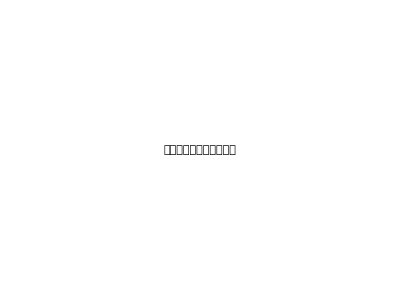
-Graphics- | -Graphics-
 | I | II | III | IV
I | 0 | 0 | 0 | 3
II | 1 | 0 | 0 | 0
III | 2 | 2 | 0 | 0
IV | 0 | 3 | 1 | 0 |

```mathematica
Grid[{{gr[0],tx[0]},{tf[0],SpanFromAbove}},ItemSize->{{1->27,2->14},{1->10,2->10}},Alignment->{{Center,Left},{Center,Left}},Spacings->{{1,0},{0,0}},Frame->True]
```

スライド2

```mathematica
m[1]=MtoG[c,0.9]
```

MtoG[{{0,0,0,3},{1,0,0,0},{2,2,0,0},{0,3,1,0}},0.9]

```mathematica
edgeforce[1]=MapIndexed[If[#>0,{#2,#1}]&,m[1],{2}]
```

MtoG[{If[{0,0,0,3}>0,{{1,1},{0,0,0,3}}],If[{1,0,0,0}>0,{{1,2},{1,0,0,0}}],If[{2,2,0,0}>0,{{1,3},{2,2,0,0}}],If[{0,3,1,0}>0,{{1,4},{0,3,1,0}}]},0.9]

```mathematica
edgeforcelabels[1]=Map[(DirectedEdge[#[[1,1]],#[[1,2]]]->Text[Style[ToString[#[[2]]],Medium]])&,Cases[edgeforce[1],_List,{2}]]
```

{}

```mathematica
style[1]=Map[(DirectedEdge[#[[1,1]],#[[1,2]]]->Thickness[#[[2]]/50])&,Cases[edgeforce[1],_List,{2}]]
```

{}

```mathematica
toAdjacency[m[1]]
```

MtoG[{If[{0,0,0,3}>0,1,0],If[{1,0,0,0}>0,1,0],If[{2,2,0,0}>0,1,0],If[{0,3,1,0}>0,1,0]},0.9]

```mathematica
gr[1]=AdjacencyGraph[toAdjacency[MtoG[c,0.9]],DirectedEdges->True,VertexLabels->vlabels,EdgeStyle->style[1],(*EdgeLabels->edgeforcelabels[1],*)ImagePadding->{{5,5},{0,5}},ImageSize->{300,300}]
```

AdjacencyGraph::matsq: Argument MtoG[{If[{0, 0, 0, 3} > 0, 1, 0], If[{1, 0, 0, 0} > 0, 1, 0], If[{2, 2, 0, 0} > 0, 1, 0], If[{0, 3, 1, 0} > 0, 1, 0]}, 0.9] at position 1 is not a non-empty square matrix.

AdjacencyGraph[MtoG[{If[{0,0,0,3}>0,1,0],If[{1,0,0,0}>0,1,0],If[{2,2,0,0}>0,1,0],If[{0,3,1,0}>0,1,0]},0.9],DirectedEdges→True,VertexLabels→{1→I,2→II,3→III,4→IV},EdgeStyle→{},ImagePadding→{{5,5},{0,5}},ImageSize→{300,300}]

```mathematica
tx[1]=Graphics[{FontSize->14,Text[Style["ランダムサーファーモデル
による結合行列",TextAlignment->Left]]}];
```

```mathematica
tf[1]=TableForm[Map[Text[Style[ToString[#],Medium]]&,m[1],{2}],TableHeadings->{nodename,nodename}]
```

MtoG[{{0, 0, 0, 3},{1, 0, 0, 0},{2, 2, 0, 0},{0, 3, 1, 0}},0.9]

```mathematica
sc[1]=Table[1/numofnodes,{numofnodes}]
```

{1/4,1/4,1/4,1/4}

```mathematica
sct[1]=TableForm[Transpose[{sc[1]}]//N,TableHeadings->{nodename,{"点数"}}]
```

| 点数
I | 0.25
II | 0.25
III | 0.25
IV | 0.25

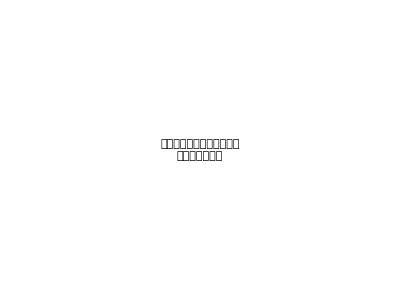
AdjacencyGraph[MtoG[{If[{0,0,0,3}>0,1,0],If[{1,0,0,0}>0,1,0],If[{2,2,0,0}>0,1,0],If[{0,3,1,0}>0,1,0]},0.9],DirectedEdges→True,VertexLabels→{1→I,2→II,3→III,4→IV},EdgeStyle→{},ImagePadding→{{5,5},{0,5}},ImageSize→{300,300}] | -Graphics-
MtoG[{{0, 0, 0, 3},{1, 0, 0, 0},{2, 2, 0, 0},{0, 3, 1, 0}},0.9] |  | 点数
I | 0.25
II | 0.25
III | 0.25
IV | 0.25

```mathematica
Grid[{{gr[1],tx[1]},{tf[1],sct[1]}},ItemSize->{{1->27,2->14},{1->10,2->10}},Alignment->{{Center,Left},{Center,Left}},Spacings->{{1,0},{0,0}},Frame->True]
```

## 作業メモおよび確認